# Setup

```mathematica
qmbInitPath = "C:\\Users\\Miguel\\Github\\libs\\QMB\\Kernel\\init.m";
Get[qmbInitPath];
SetDirectory[NotebookDirectory[]];
```

```mathematica
LaunchKernels[12];
```

```mathematica
Names["QMB`*"]
```

{AnalyticalNumberVarianceGOE,AnalyticalNumberVarianceGUE,AnalyticalNumberVariancePoisson,ARQMHamiltonian,BlochVector,BoseHubbardHamiltonian,BoseHubbardHilbertSpaceDimension,BosonEscapeKrausOperators,BosonicPartialTrace,Braket,ClassicalMapeo,ClassicalStep,ClassicalToDisk,ClassicalToSphere,COEAsymptoticSigma2,COESFFAnalytical,coherentstate,CommutationQ,CompileLevelCounter,CompileSFF,ComplexSpacingRatios,ComplexToPolar,ComputeSigma2Sliding,Concurrence,DensityMatrix,Dyad,EigenvectorQ,EmpiricalKLDivergence,EnsembleSFF,EnsembleSigma2,EvaluateSpectrumSigma2,FixCkForStateEvoultion,Floq,Floqb,Floqbn,Floqn,Floqsym,FluctuationPowerSpectrum,FockBasis,FockBasisIndex,FockBasisStateAsColumnVector,FuzzyMeasurement,FuzzyMeasurementChannel,GenerateCOEEnsemble,generateCoherentStateCompiler,GenerateGinibreMatrix,GenerateQKTEnsemble,generateSpinOperators,GetFluctuations,GetQKTParityEigensystem,GetQKTParitySpectra,HaarRandomState,HilbertSpaceDim,InitializationBosonicPartialTrace,InitializeVariables,IntWignerCOE,IPR,KetInComputationalBasisFromVector,KineticTermBoseHubbardHamiltonian,KLDivergence,KroneckerVectorProduct,kthOrderSpacings,LengthSpectrum,LevelSpacingDistribution,MatrixCommutator,MatrixPartialTrace,MatrixPartialTraceFromPureState,MeanLevelSpacingRatio,MutuallyCommutingSetQ,NNSpacings,NormalizedSpacingRatios,NumberVariance,ParitySectorIndices,PartialTranspose,Pauli,PoolSpacingRatios,PoolSpacings,PotentialTermBoseHubbardHamiltonian,PrCOE,PrCUE,PrPoisson,Purity,QuantumTexture,Qubit,QubitStateFromBlochVector,RandomChainProductState,RandomCOESpectrum,RandomQubitState,RandomSU2Parameters,RandomSU2Rotation,RatiosDistribution,RatiosDistributionPoisson,RenyiEntropy,Reshuffle,SingleSFF,SingleSpectrumSigma2,SortFockBasis,SpacingRatios,SpectralFormFactor,SpectralFormFactorRMT,StateEvolution,SU2Rotation,SU2RotationParameters,SuperoperatorFromU,SwapMatrix,SymmetricSubspace,Tag,TimeAveragedSFF,Unfold,UnfoldLinear,ValidateUnfolding,VectorFromKetInComputationalBasis,WeylMatrix,WignerCOE,ω}

# Hamiltonian

```mathematica
L=8;
J=1.;
hx=1.05;
hz=0.5;
H=IsingHamiltonian[hx,hz,J,L];
evals=Eigenvalues[Normal[H]];
```

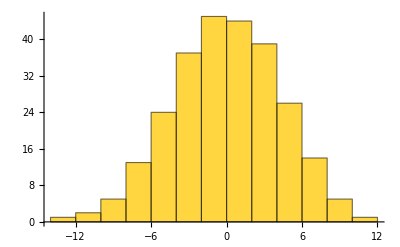

```mathematica
Histogram[evals,FrameLabel->{"E","DOS"}]
```

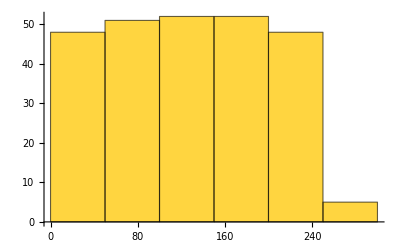

```mathematica
newevals=Unfold[evals];
Histogram[newevals["UnfoldedLevels"],FrameLabel->{"E","DOS"}]
```

# State

```mathematica
RandomChainProductState[3]
```

{0.493807+0. ⅈ,0.113179-0.349047 ⅈ,0.210036-0.098558 ⅈ,-0.0215257-0.171053 ⅈ,0.181342+0.501027 ⅈ,0.395713-0.0133472 ⅈ,0.177131+0.176913 ⅈ,0.165649-0.0846566 ⅈ}

# Entanglement entropy

```mathematica
Clear[pageEntropy];
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb))
```

```mathematica
ClearAll[entanglement];
entanglement[psi_, LA_, L_] := Module[{mat, s, p},
    mat = ArrayReshape[psi, {2^LA, 2^(L - LA)}];
    s = SingularValueList[mat];
    p = s^2;
    p = Select[p, # > 10^-14 &];
    -Chop[Total[p Log[p]]]
];
```

```mathematica
L=4;
ini=RandomChainProductState[L];
```

```mathematica
entanglement[ini,1,L]
```

0

# Time evolution

```mathematica
L=6;
```

```mathematica
J=1.;
hx=1.05;
hz=0.5;
```

```mathematica
H=IsingHamiltonian[hx,hz,J,L];
```

```mathematica
{evals,evecs}=Transpose[Sort[Transpose[Eigensystem[Normal[H]]]]];
```

```mathematica
psi0=RandomChainProductState[L];
```

```mathematica
coeff=Conjugate[evecs].psi0;
```

```mathematica
Clear[psit];
psit[t_]:=Transpose[evecs].(Exp[-I evals t] coeff);
```

```mathematica
tlist=Table[i,{i,0,50,0.1}];
```

```mathematica
data=ParallelTable[
With[{psi=Transpose[evecs].(Exp[-I evals t] coeff)},
{t,entanglement[psi,L/2,L]}],
{t,tlist}];
```

```mathematica
pagevalue=Plot[pageEntropy[L/2,L/2],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]];
```

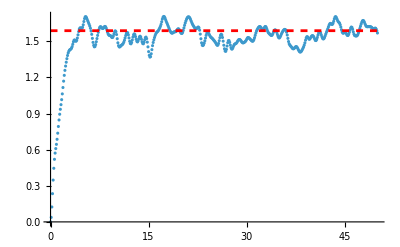

```mathematica
Show[ListPlot[data,PlotRange->All],pagevalue]
```

# Reflection operator

```mathematica
ClearAll[reflectionOperator];
reflectionOperator[L_Integer]:=Module[{dim,perm},dim=2^L;
perm=Table[1+FromDigits[Reverse[IntegerDigits[j-1,2,L]],2],{j,dim}];
SparseArray[(#->1)&/@Transpose[{perm,Range[dim]}],{dim,dim}]];
```

```mathematica
ClearAll[reflectionSectorBases];
reflectionSectorBases[L_Integer]:=Module[{dim,perm,plusRules={},minusRules={},np=0,nm=0,j,k},
dim=2^L;
perm=Table[1+FromDigits[Reverse[IntegerDigits[j-1,2,L]],2],{j,dim}];
Do[k=perm[[j]];
Which[j<k,np++;
AppendTo[plusRules,{j,np}->1/Sqrt[2]];
AppendTo[plusRules,{k,np}->1/Sqrt[2]];
nm++;
AppendTo[minusRules,{j,nm}->1/Sqrt[2]];
AppendTo[minusRules,{k,nm}->-1/Sqrt[2]],j==k,np++;
AppendTo[plusRules,{j,np}->1]],{j,dim}];
<|"Even"->SparseArray[plusRules,{dim,np}],"Odd"->SparseArray[minusRules,{dim,nm}]|>];
```

```mathematica
J=1.;
hx=1.05;
hz=0.5;
```

```mathematica
H=IsingHamiltonian[hx,hz,J,L];
```

```mathematica
R=reflectionOperator[L];
```

```mathematica
R//Dimensions
```

{256,256}

```mathematica
Norm[H.R-R.H]
```

0.

```mathematica
bases=reflectionSectorBases[L];
Bp=bases["Even"];
Bm=bases["Odd"];
```

```mathematica
Chop[ConjugateTranspose[Bp].Bp]
Chop[ConjugateTranspose[Bm].Bm]
Chop[ConjugateTranspose[Bp].Bm]
```

SparseArray[…]

SparseArray[…]

SparseArray[…]

```mathematica
Hp=Chop[ConjugateTranspose[Bp].H.Bp];
Hm=Chop[ConjugateTranspose[Bm].H.Bm];
```

```mathematica
Dimensions[H]
Dimensions[Hp]
Dimensions[Hm]
```

{256,256}

{136,136}

{120,120}

```mathematica
ClearAll[sortedEigensystem];
sortedEigensystem[M_]:=Module[{evals,evecs,ord},
{evals,evecs}=Eigensystem[Normal[M]];
ord=Ordering[evals];
{evals[[ord]],evecs[[ord]]}];
```

```mathematica
{evalsP,evecsP}=sortedEigensystem[Hp];
{evalsM,evecsM}=sortedEigensystem[Hm];
```

```mathematica
(*Lift eigenvectors back to the full Hilbert space*)
fullEvecsP=(Bp.#)&/@evecsP;
fullEvecsM=(Bm.#)&/@evecsM;
```

```mathematica
parityResidualP=Norm[R.#-#]&/@fullEvecsP;
parityResidualM=Norm[R.#+#]&/@fullEvecsM;
```

```mathematica
Max[parityResidualP]
Max[parityResidualM]
```

0.

0.

```mathematica
parityP=Chop[Conjugate[#].(R.#)&/@fullEvecsP];
parityM=Chop[Conjugate[#].(R.#)&/@fullEvecsM];
```

```mathematica
Union[parityP]
Union[parityM]
```

{1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

{-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.,-1.}

# Full entropy evolution

```mathematica
ClearAll[sortedEigensystem];
sortedEigensystem[M_]:=Module[{evals,evecs,ord},
{evals,evecs}=Eigensystem[Normal[M]];
ord=Ordering[evals];
{evals[[ord]],evecs[[ord]]}];
```

```mathematica
L=8;
J=1.;
hz=1;
```

```mathematica
hx=0.5;
H=IsingHamiltonian[hx,hz,J,L];
```

```mathematica
Hp=Chop[ConjugateTranspose[Bp].H.Bp];
Hm=Chop[ConjugateTranspose[Bm].H.Bm];
```

```mathematica
{evalsP,evecsP}=sortedEigensystem[Hp];
{evalsM,evecsM}=sortedEigensystem[Hm];
```

```mathematica
psi0=RandomChainProductState[L];
```

```mathematica
psi0P=ConjugateTranspose[Bp].psi0;
psi0M=ConjugateTranspose[Bm].psi0;
```

```mathematica
Norm[psi0P]^2+Norm[psi0M]^2
```

1.

```mathematica
coeffP=Conjugate[evecsP].psi0P;
coeffM=Conjugate[evecsM].psi0M;
```

```mathematica
ClearAll[psit];
psit[t_]:=Bp.(Transpose[evecsP].(Exp[-I evalsP t] coeffP))+Bm.(Transpose[evecsM].(Exp[-I evalsM t] coeffM));
```

```mathematica
tlist=Table[i,{i,0,10000,1.}];
tlist//Length
```

10001

```mathematica
data=ParallelTable[With[{psi=psit[t]},{t,entanglement[psi,L/2,L]}],{t,tlist}];
```

```mathematica
pagevalue=Plot[pageEntropy[L/2,L/2],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Red,Dashed]];
```

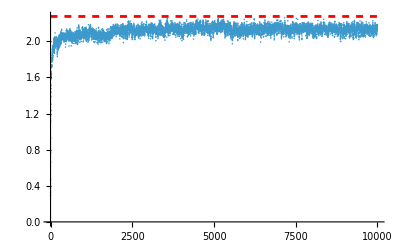

```mathematica
Show[ListPlot[data,PlotRange->All],pagevalue,PlotRange->All]
```

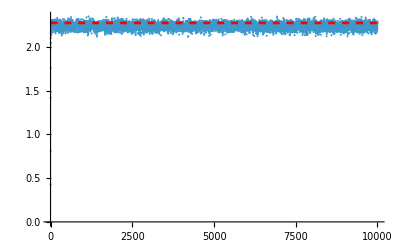

```mathematica
Show[ListPlot[data,PlotRange->All],pagevalue,PlotRange->All]
```

```mathematica
evals=Sort[Join[evalsP,evalsM]];
spectrum=SortBy[Join[({#,+1}&/@evalsP),({#,-1}&/@evalsM)],First];
```

# plots

```mathematica
ListLogLinearPlot[{Transpose[{tlist,entropy[[q]]}],MovingAverage[Transpose[{tlist,entropy[[q]]}],200]},PlotStyle->{Directive[Gray,Opacity[0.10]],Directive[reds[[h]],Opacity[1]]},PlotRange->{{tlist[[1]],tlist[[-1]]},All},Joined->{True,False},ImageSize->800,PlotTheme->"Detailed",PlotTheme->"Detailed",FrameStyle->Directive[Black,20],PlotLabel->Style["PBC, L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = 1",35,Black],FrameLabel->{Style["t",25,Black],Style["Svn(t)",25,Black]}]
```

# Full entropy evolution packed

```mathematica
ClearAll[sortedEigensystem];
sortedEigensystem[M_]:=Module[{evals,evecs,ord},
{evals,evecs}=Eigensystem[Normal[M]];
ord=Ordering[evals];
{evals[[ord]],evecs[[ord]]}];
```

```mathematica
L=8;
J=1.;
hz=1;
```

```mathematica
hx=0.01;
H=IsingHamiltonian[hx,hz,J,L];
```

```mathematica
Hp=Chop[ConjugateTranspose[Bp].H.Bp];
Hm=Chop[ConjugateTranspose[Bm].H.Bm];
```

```mathematica
{evalsP,evecsP}=sortedEigensystem[Hp];
{evalsM,evecsM}=sortedEigensystem[Hm];
```

```mathematica
psi0=RandomChainProductState[L];
```

```mathematica
psi0P=ConjugateTranspose[Bp].psi0;
psi0M=ConjugateTranspose[Bm].psi0;
```

```mathematica
coeffP=Conjugate[evecsP].psi0P;
coeffM=Conjugate[evecsM].psi0M;
```

```mathematica
VP=Bp.Transpose[evecsP];
VM=Bm.Transpose[evecsM];
```

```mathematica
Vfull=Join[VP,VM,2];
evalsFull=Join[evalsP,evalsM];
coeffFull=Join[coeffP,coeffM];
```

```mathematica
Norm[Vfull.coeffFull-psi0]
```

2.87581×10^-14

```mathematica
Vfull=Developer`ToPackedArray[N[Vfull]];
evalsFull=Developer`ToPackedArray[N[evalsFull]];
coeffFull=Developer`ToPackedArray[N[coeffFull]];
```

```mathematica
Developer`PackedArrayQ/@{Vfull,evalsFull,coeffFull}
```

{True,True,True}

```mathematica
V=Developer`ToPackedArray[Re[Vfull]];
```

```mathematica
cR=Developer`ToPackedArray[Re[coeffFull]];
cI=Developer`ToPackedArray[Im[coeffFull]];

cosE=Developer`ToPackedArray[Cos[evalsFull]];
sinE=Developer`ToPackedArray[Sin[evalsFull]];
```

```mathematica
ClearAll[phaseStepC];
phaseStepC=Compile[{{aR,_Real,1},{aI,_Real,1},{cosE,_Real,1},{sinE,_Real,1}},Module[{newR,newI},
newR=aR*cosE+aI*sinE;
newI=aI*cosE-aR*sinE;
{newR,newI}],CompilationTarget->"C",RuntimeOptions->"Speed"];
```

```mathematica
ClearAll[entropyFromSVC];
entropyFromSVC=Compile[{{sv,_Real,1}},Module[{sum=0.,p=0.,i,n},
n=Length[sv];
For[i=1,i<=n,i++,p=sv[[i]]*sv[[i]];
If[p>1.*^-14,sum-=p*Log[p]];];
sum],CompilationTarget->"C",RuntimeOptions->"Speed"];
```

```mathematica
L=8;
```

```mathematica
(* ============================================================*)
(*Optimized single-state long-time entropy evolution*)
(* ============================================================*)
LA=L/2;
dA=2^LA;
dB=2^(L-LA);
```

```mathematica
(*------------------------------------------------------------*)
(*Combine the already symmetry-resolved eigenbases*)
(*------------------------------------------------------------*)
VP=Bp.Transpose[evecsP];
VM=Bm.Transpose[evecsM];

Vfull=Developer`ToPackedArray[N@Join[VP,VM,2]];

evalsFull=Developer`ToPackedArray[N@Join[evalsP,evalsM]];

coeffFull=Developer`ToPackedArray[N@Join[coeffP,coeffM]];

(*Check reconstruction at t=0*)
Print["Initial-state reconstruction error = ",Norm[Vfull.coeffFull-psi0]];
```

Initial-state reconstruction error = 2.87581×10^-14

```mathematica
(*------------------------------------------------------------*)
(*This model should have a real eigenbasis*)
(*------------------------------------------------------------*)
Print["Max imaginary part of Vfull = ",Max[Abs[Im[Vfull]]]];
V=Developer`ToPackedArray[Re[Vfull]];
```

Max imaginary part of Vfull = 0

```mathematica
(*------------------------------------------------------------*)
(*Initial coefficients and one-step phases*)
(*------------------------------------------------------------*)
cR=Developer`ToPackedArray[Re[coeffFull]];
cI=Developer`ToPackedArray[Im[coeffFull]];
cosE=Developer`ToPackedArray[Cos[evalsFull]];
sinE=Developer`ToPackedArray[Sin[evalsFull]];
```

```mathematica
(*------------------------------------------------------------*)
(*C-compiled one-step eigenphase evolution*)
(*------------------------------------------------------------*)
ClearAll[phaseStepC];
phaseStepC=Compile[{{aR,_Real,1},{aI,_Real,1},{cosE,_Real,1},{sinE,_Real,1}},Module[{newR,newI},newR=aR*cosE+aI*sinE;
newI=aI*cosE-aR*sinE;
{newR,newI}],CompilationTarget->"C",RuntimeOptions->"Speed"];
(*------------------------------------------------------------*)
(*C-compiled entropy reduction*)
(*------------------------------------------------------------*)
ClearAll[entropyFromSVC];
entropyFromSVC=Compile[{{sv,_Real,1}},Module[{sum=0.,p=0.,i,n},n=Length[sv];
For[i=1,i<=n,i++,p=sv[[i]]*sv[[i]];
If[p>1.*^-14,sum-=p*Log[p]];];
sum],CompilationTarget->"C",RuntimeOptions->"Speed"];
(*------------------------------------------------------------*)
(*Periodic exact reseeding*)
(*------------------------------------------------------------*)
ClearAll[reseedC];
reseedC=Compile[{{cR,_Real,1},{cI,_Real,1},{energies,_Real,1},{t,_Real}},Module[{ct,st},ct=Cos[energies*t];
st=Sin[energies*t];
{cR*ct+cI*st,cI*ct-cR*st}],CompilationTarget->"C",RuntimeOptions->"Speed"];
(*------------------------------------------------------------*)
(*Entropy:SVD stays in optimized Wolfram numerical LA*)
(*------------------------------------------------------------*)
ClearAll[entropyFast];
entropyFast[psiR_,psiI_]:=Module[{mat,sv},mat=ArrayReshape[psiR+I psiI,{dA,dB}];
sv=SingularValueList[mat];
entropyFromSVC[sv]];
```

```mathematica
(*------------------------------------------------------------*)
(*Long-time sequential evolution*)
(*------------------------------------------------------------*)
tmax=10^5;
resetEvery=100000;

aR=cR;
aI=cI;
```

```mathematica
entropy=Table[
(*Computational-basis state*)
psiR=V.aR;
psiI=V.aI;
(*Half-chain von Neumann entropy*)
SvN=entropyFast[psiR,psiI];
(*Advance to t+1*)
If[t<tmax,If[Mod[t+1,resetEvery]==0,{aR,aI}=reseedC[cR,cI,evalsFull,N[t+1]],{aR,aI}=phaseStepC[aR,aI,cosE,sinE]]];
SvN,{t,0,tmax}];
entropy=Developer`ToPackedArray[entropy];
```

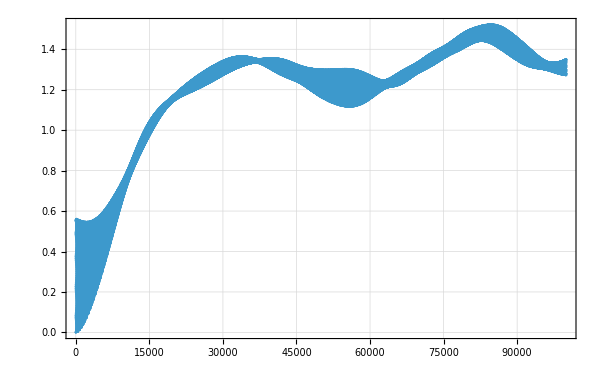

```mathematica
ListPlot[Transpose[{Range[0,tmax],entropy}],PlotRange->All,PlotTheme->"Detailed",ImageSize->600]
```

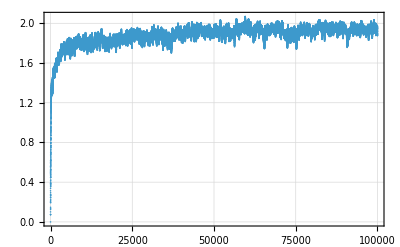

```mathematica
ListPlot[Transpose[{Range[0,tmax],entropy}],PlotRange->All,PlotTheme->"Detailed"]
```

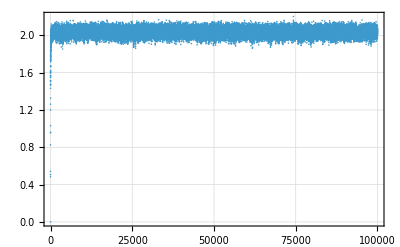

```mathematica
ListPlot[Transpose[{Range[0,tmax],entropy}],PlotRange->All,PlotTheme->"Detailed"]
```

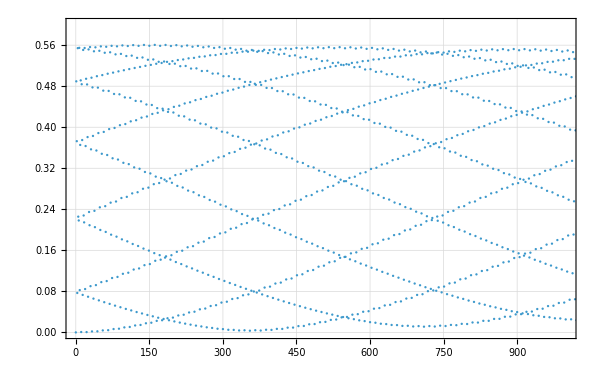

```mathematica
ListPlot[Transpose[{Range[0,tmax],entropy}],PlotRange->{{0,1000},{0,0.6}},PlotTheme->"Detailed",ImageSize->600]
```

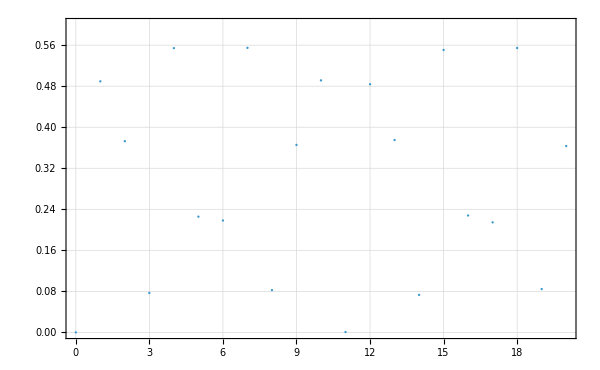

```mathematica
ListPlot[Transpose[{Range[0,tmax],entropy}],PlotRange->{{0,20},{0,0.6}},PlotTheme->"Detailed",ImageSize->600]
```